```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pi/Desktop

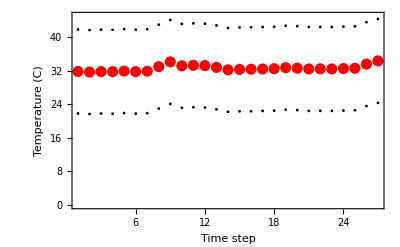

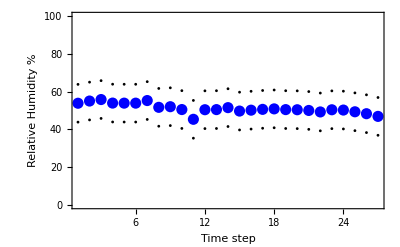

```mathematica
t=Flatten[Import["/home/pi/Desktop/temperature.txt","Data"]];
r=Flatten[Import["/home/pi/Desktop/rh.txt","Data"]];
ListLinePlot[{t-10,t,t+10},PlotRange->{All,{0,45}},Frame->True,FrameStyle->Black,PlotStyle->{{Black,PointSize[0.005]},{PointSize[.02],Red},{Black,PointSize[0.005]}},FrameLabel->{"Time step", "Temperature (C)"},Joined->False]

ListLinePlot[{r-10,r,r+10},PlotRange->{All,{0,100}},Frame->True,FrameStyle->Black,PlotStyle->{{Black,PointSize[0.005]},{PointSize[.02],Blue},{Black,PointSize[0.005]}},FrameLabel->{"Time step", "Relative Humidity %"},Joined->False]
```

```mathematica
sh=DeviceOpen["SenseHAT"]
```

DeviceObject[…]

```mathematica
DeviceRead[sh, "Temperature"]
```

38.6583 °C

#### Shift + Enter runs the cell below 5 times

```mathematica
Do[
DeviceWrite[sh,{"Suvi-cat", "ScrollSpeed"->0.08}],{i,5}]
```

$Aborted

```mathematica
obj=DeviceOpen["weatherstation"]
```

DeviceOpen::noclass: A driver for weatherstation was not found on your local computer or currently available paclet sites. If you can locate the driver, add the driver directory to $Path or load the driver directly with Get. If you cannot locate the driver, contact the device manufacturer or create a driver using the Wolfram Device Framework. See http://devices.wolfram.com for more information.

$Failed